```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[] <> "\\Code\\Output"];
```

# Подготовка таблички нормы ошибок методов

```mathematica
(* Модуль возвращающий индекс первого элемента table, который больше заданного числа*)
FindIndex[table_, num_]:=Module[{index},index=FirstPosition[table,_?(#>num&)];
If[index===Missing["NotFound"],Missing["NotFound"],index[[1]]]]
```

```mathematica
(* Функция, возвращающая график решения метода в момент t *)
LTEPlotDATAtime[data_, sol_,  time_ :0, ifjoin_: False]:= Module[{plotdata},
(*coord1 = FindIndex[data[[1]][[2;;]], -1];
coord2 = FindIndex[data[[1]][[2;;]], 1];*)

plotdata = ListPlot[Table[{data[[1]][[coord]],data[[time]][[coord]]},{coord, 2,Length@data[[1]]-1, 1}
], Joined->ifjoin, PlotRange->{{-1, 1},Automatic}, AxesLabel->{"x", "u(x, t)"},
   PlotStyle -> Black, ImageSize->{300,300},LabelStyle->{FontSize->15},
AspectRatio->1, Frame->True,AxesOrigin->{0,0}, GridLines->Automatic(*, PlotLabel->"Численное"*)];
plotdata
]


(* Функция, возвращающая график аналитического решения  в момент t *)
LTEPlotSOLtime[data_, sol_,  time_:0 , ifjoin_: False]:= Module[{plotsol, coord1, coord2},
(*
coord1 = FindIndex[data[[1]][[2;;]], -1];
coord2 = FindIndex[data[[1]][[2;;]], 1];*)

plotsol = ListPlot[Table[{data[[1]][[coord]], Evaluate[sol /. {t-> data[[time]][[1]], x -> data[[1]][[coord]]}]}, {coord,2,Length@data[[1]]-1, 1}
], Joined->ifjoin, PlotRange->{{-1, 1},Automatic}, AxesLabel->{"x", "u(x, t)"},   PlotStyle -> Black, ImageSize->{300,300},LabelStyle->{FontSize->15},AspectRatio->1, Frame->True,AxesOrigin->{0,0}, GridLines->Automatic (*, PlotLabel->"Точное"*)];
plotsol
]

(* Функция, возвращающая график нормы ошибки метода на всем отрезке времени *)
LTEPlotERR[data_, sol_,  ifjoin_: False]:= Module[{ploterr,tab, norm, coord1, coord2},
(*coord1 = FindIndex[data[[1]][[2;;]], -1];
coord2 = FindIndex[data[[1]][[2;;]], 1];*)



tab = Table[{data[[time]][[1]],
Sum[Abs[data[[time]][[coord]] - Evaluate[sol/.{x->data[[1]][[coord]], t-> data[[time]][[1]]}]], {coord, 2,Length@data[[1]]-1, 1}]},

 {time, 2,Length@data, 1}];
norm = Sum[tab[[i]][[2]], {i, 1, Length@tab}];
Print[norm];


ploterr = ListPlot[tab,
Joined->False, PlotRange->{{0, data[[-1]][[1]]},Automatic}, AxesLabel->{"time", "ERR"},PlotStyle -> Black, ImageSize->{300,300},LabelStyle->{FontSize->15},AspectRatio->1,AxesOrigin->{0,0}, Frame->True, GridLines->Automatic(*, PlotLabel->"Ошибка"*)];
ploterr

]

(* Функция, вызывающая все предыдущие функции для анализа метода *)
LTEPlottimeALL[data_, sol_,  time_: 0, text_:" "]:= Module[{ploterr,coord1, coord2},
Print[text];
LTEPlotDATAtime[data, sol,time, False]
LTEPlotSOLtime[data, sol,time,True]
LTEPlotERR[data, sol,False]
]
```

545.49

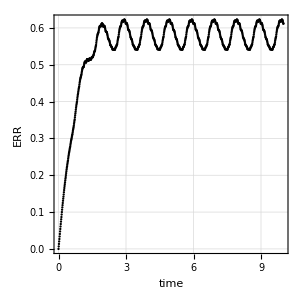
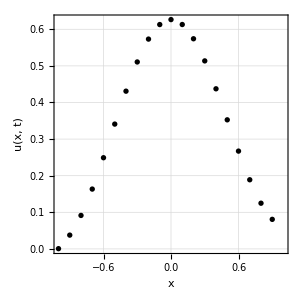
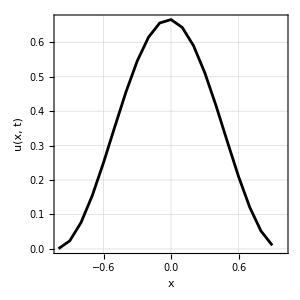

{0,-1,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}

{0.1,0.0163145,0.0110384,0.0248233,0.0665255,0.136455,0.227671,0.329909,0.432445,0.525155,0.599044,0.646923,0.664112,0.648924,0.602843,0.530381,0.43863,0.336572,0.234197,0.141526,0.0676309,0.0197442}

```mathematica
(* Тест 1 *)
(*data1= Import["test1\\test1_LD2e.txt", "Table"];
data2= Import["test1\\test1_LD2i.txt", "Table"];
data3= Import["test1\\test1_LD3e.txt", "Table"];
(*data4= Import["test1\\test1_LD3i.txt", "Table"];*)
data5= Import["test1\\test1_Lax.txt", "Table"];
data6= Import["test1\\test1_LaxWen.txt", "Table"];*)
sol = 1/2 (1-t+x);

data= Import["test4\\test4_LD3i.txt", "Table"];
(*sol = 1/2 (1-t+x);*)
sol =1/3 (1-Cos[π (1-t+x)]);
mytime = 1000;
LTEPlottimeALL[data, sol, mytime, ""]
data4[[1]]
data4[[12]]
```

```mathematica
(* Тест 4 *)
(*data1= Import["test4\\test4_LD2e.txt", "Table"];
data2= Import["test4\\test4_LD2i.txt", "Table"];
data3= Import["test4\\test4_Lax.txt", "Table"];
data4 = Import["test4\\test4_LaxWen.txt", "Table"];
data5= Import["test4\\test4_LD3e.txt", "Table"];
sol =1/3 (1-Cos[π (1-t+x)]);*)
```

```mathematica
(* Функция, возвращающая график нормы ошибки метода на всем отрезке времени *)
LTEerr[data_, sol_, h_, tau_, text_: ""]:= Module[{tab, norm},




tab = Table[ Sum[Abs[data[[time]][[coord]] - Evaluate[sol/.{x->data[[1]][[coord]], t-> data[[time]][[1]]}]], {coord, 2,Length@data[[1]]-1, 1}],{time, 2,Length@data, 1}];
norm = Sum[tab[[i]], {i, 1, Length@tab}] * h * tau;
Print["Норма ошибки ", text, " в L1: ",norm];

]
data1= Import["test1\\test1_LD2e.txt", "Table"];
data2= Import["test1\\test1_LD2i.txt", "Table"];
data3= Import["test1\\test1_LD3e.txt", "Table"];
data4= Import["test1\\test1_LD3i.txt", "Table"];
data5= Import["test1\\test1_Lax.txt", "Table"];
data6= Import["test1\\test1_LaxWen.txt", "Table"];
sol = 1/2 (1-t+x);
h = 0.1;
tau = 0.05;
LTEerr[data1, sol, h, tau, "LD2e"]
LTEerr[data2, sol, h, tau, "LD2i"]
LTEerr[data3, sol, h, tau, "LD3e"]
(*LTEerr[data4, sol,h, tau, "LD3i"]*)
LTEerr[data5, sol, h, tau, "Lax"]
LTEerr[data6, sol,h, tau, "LaxWen"]
```

Норма ошибки LD2e в L1: 1.00182×10^-14

Норма ошибки LD2i в L1: 1.00241×10^-14

Норма ошибки LD3e в L1: 97.7198

Норма ошибки Lax в L1: 1.00349×10^-14

Норма ошибки LaxWen в L1: 1.00232×10^-14

```mathematica
data1= Import["test4\\test4_LD2e.txt", "Table"];
data2= Import["test4\\test4_LD2i.txt", "Table"];
data3= Import["test4\\test4_LD3e.txt", "Table"];
data4 = Import["test4\\test4_LD3i.txt", "Table"];
data5= Import["test4\\test4_Lax.txt", "Table"];
data6= Import["test4\\test4_LaxWen.txt", "Table"];

sol =1/3 (1-Cos[π (1-t+x)]);
h = 0.01;
tau = 0.005;
LTEerr[data1, sol, h, tau, "LD2e"]
LTEerr[data2, sol, h, tau, "LD2i"]
LTEerr[data3, sol, h, tau, "LD3e"]
LTEerr[data4, sol,h, tau, "LD3i"]
LTEerr[data5, sol, h, tau, "Lax"]
LTEerr[data6, sol,h, tau, "LaxWen"]
```

Норма ошибки LD2e в L1: 0.0640625

Норма ошибки LD2i в L1: 0.0742498

Норма ошибки LD3e в L1: 0.147403

Норма ошибки LD3i в L1: 0.0272745

Норма ошибки Lax в L1: 0.178701

Норма ошибки LaxWen в L1: 0.0113259